```mathematica
SetDirectory[NotebookDirectory[]];
```

# h_scaling

## data

```mathematica
mpi=Flatten[Import["../mpi/buffer/mPion.dat"]];
fpi=Flatten[Import["../mub0/buffer/fpi.dat"]];
h=Flatten[Import["../mub0/buffer/c.dat"]]*197.33^3;
datamub0=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
datamub0linear=Transpose[{h[[2;;Length[h]]],fpi[[2;;Length[h]]]}];

mpi=Flatten[Import["../mpi/buffer/mPion.dat"]];
fpi=Flatten[Import["../mub550/buffer/fpi.dat"]];
h=Flatten[Import["../mub550/buffer/c.dat"]]*197.33^3;
datamub550=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
datamub550linear=Transpose[{h[[2;;Length[h]]],fpi[[2;;Length[h]]]}];
```

## Pre Fit

```mathematica
fitb=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fita=Transpose[{Log[h[[2;;Length[h]-2]]],Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[1]][[2]],{i,2,Length[h]-2}]]}];
```

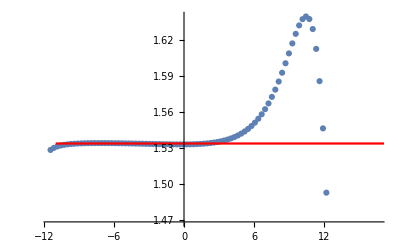

```mathematica
Show[ListPlot[fita],ListLinePlot[{{-11,1.534},{20,1.534}},PlotStyle->Red]]
```

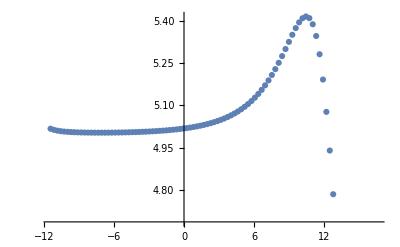

```mathematica
ListPlot[fitb]
```

## Fit

```mathematica
(*A=Exp[1.532];*)
δ=5.0;
delta=5.0;
beta=0.4;
nu=0.804;
omega=0.7459;
θH=(nu*omega)/(beta*delta);
A1=Exp[1.532];
am1=-0.003;
fitfun=A x^(1/δ)(1+am x^θH);
fitfun2=A x^(1/δfit)(1+am x^θH);
fitfun3=A x^(1/δfit)(1+am1 x^θH);
fitfun4=A1 x^(1/delta)(1+am1 x^θH1);
```

```mathematica
fitA=Transpose[{h[[2;;Length[h]-2]],Flatten[Table[NonlinearModelFit[datamub0linear[[i-1;;i+1]],fitfun,{A,am},x][[1]][[2]][[1]][[2]],{i,2,Length[h]-2}]]}];
fitam=Transpose[{h[[2;;Length[h]-2]],Flatten[Table[NonlinearModelFit[datamub0linear[[i-1;;i+1]],fitfun,{A,am},x][[1]][[2]][[2]][[2]],{i,2,Length[h]-2}]]}];
```

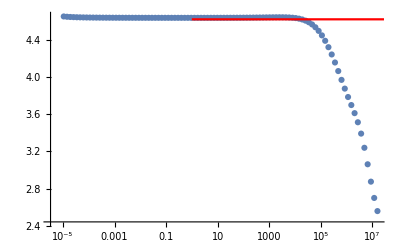

```mathematica
Show[ListPlot[fitA,ScalingFunctions->{"Log"},PlotRange->All],ListLinePlot[{{10^-6,Exp[1.532]},{10^6,Exp[1.532]}},PlotStyle->Red]]
```

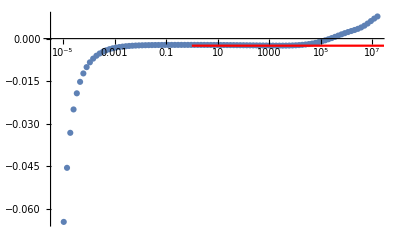

```mathematica
Show[ListPlot[fitam,ScalingFunctions->{"Log"},PlotRange->All],ListLinePlot[{{10^-6,-0.0025},{10^6,-0.0025}},PlotStyle->Red,PlotRange->All]]
```

```mathematica
fitdelta=Transpose[{h[[3;;Length[h]-3]],Flatten[Table[NonlinearModelFit[datamub0linear[[i-2;;i+2]],fitfun2,{A,δfit,am},x][[1]][[2]][[2]][[2]],{i,3,Length[h]-3}]]}];
```

NonlinearModelFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，NonlinearModelFit::cvmit 的进一步输出将被抑制.

NonlinearModelFit::sszero: 搜索中的步长比由 PrecisionGoal 选项规定的容差小，但是梯度大于由 AccuracyGoal 选项指定的容差. 有可能该方法会停在一个并非局部最小值的点上.

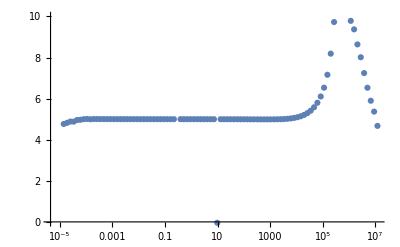

```mathematica
Show[ListPlot[fitdelta,ScalingFunctions->{"Log"},PlotRange->{All,{0,10}}]]
```

```mathematica
fitdeltampi=Transpose[{mpi[[3;;Length[h]-3]],Transpose[fitdelta][[2]]}];
```

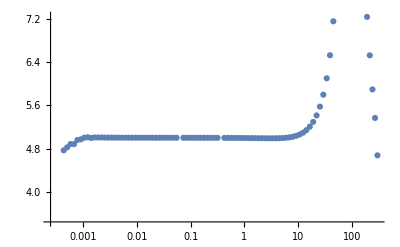

```mathematica
ListPlot[fitdeltampi,ScalingFunctions->{"Log"}]
```

```mathematica
Export["NLOdelta.dat",fitdeltampi]
```

NLOdelta.dat

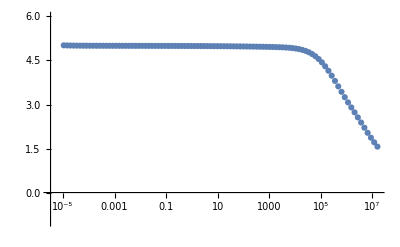

```mathematica
fitdelta=Transpose[{h[[2;;Length[h]-2]],Flatten[Table[NonlinearModelFit[datamub0linear[[i-1;;i+1]],fitfun3,{A,δfit},x][[1]][[2]][[2]][[2]],{i,2,Length[h]-2}]]}];
ListPlot[fitdelta,ScalingFunctions->{"Log"},PlotRange->{All,{-1,6}}]
```

```mathematica
fitdelta=Transpose[{h[[2;;Length[h]-2]],Flatten[Table[NonlinearModelFit[datamub0linear[[i-1;;i+1]],fitfun4,{θH1},x][[1]][[2]][[1]][[2]],{i,2,Length[h]-2}]]}];
```

LinearAlgebra`BLAS`TRSV::oflow: 在计算过程中，碰到机器精度溢出.

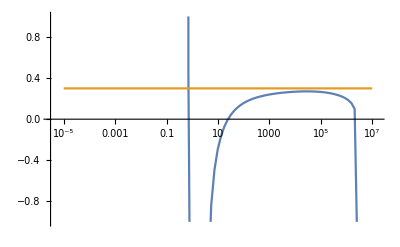

```mathematica
ListLinePlot[{fitdelta,{{10^-5,0.2998},{10^7,0.2998}}},ScalingFunctions->{"Log"},PlotRange->{All,{-1,1}}]
```

## finalFit

```mathematica
(*A=Exp[1.532];*)
δ=5.0;
delta=5.0;
beta=0.4;
nu=0.804;
omega=0.7459;
θH=(nu*omega)/(beta*delta);
A1=Exp[1.532];
am1=-0.003;
fitfun=A x^(1/δ)(1+am x^θH);
fitfun2=A x^(1/δfit)(1+am x^θH);
fitfun3=A x^(1/δfit)(1+am1 x^θH);
fitfun4=A1 x^(1/delta)(1+am1 x^θH1);
```

```mathematica
fitdelta=Transpose[{h[[3;;Length[h]-3]],Flatten[Table[NonlinearModelFit[datamub0linear[[i-2;;i+2]],fitfun2,{A,δfit,am},x][[1]][[2]][[2]][[2]],{i,3,Length[h]-3}]]}];
```

NonlinearModelFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，NonlinearModelFit::cvmit 的进一步输出将被抑制.

NonlinearModelFit::sszero: 搜索中的步长比由 PrecisionGoal 选项规定的容差小，但是梯度大于由 AccuracyGoal 选项指定的容差. 有可能该方法会停在一个并非局部最小值的点上.

```mathematica
Show[ListPlot[fitdelta,ScalingFunctions->{"Log"},PlotRange->{All,{0,10}}]]
```

-Graphics-

```mathematica
fitdeltampi=Transpose[{mpi[[3;;Length[h]-3]],Transpose[fitdelta][[2]]}];
```

```mathematica
ListPlot[fitdeltampi,ScalingFunctions->{"Log"}]
```

-Graphics-

```mathematica
Export["NLOdelta.dat",fitdeltampi]
```

NLOdelta.dat

```mathematica
fitdeltamub550=Transpose[{h[[3;;Length[h]-3]],Flatten[Table[NonlinearModelFit[datamub550linear[[i-2;;i+2]],fitfun2,{A,δfit,am},x][[1]][[2]][[2]][[2]],{i,3,Length[h]-3}]]}];
```

NonlinearModelFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，NonlinearModelFit::cvmit 的进一步输出将被抑制.

NonlinearModelFit::sszero: 搜索中的步长比由 PrecisionGoal 选项规定的容差小，但是梯度大于由 AccuracyGoal 选项指定的容差. 有可能该方法会停在一个并非局部最小值的点上.

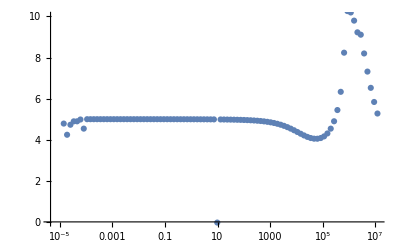

```mathematica
Show[ListPlot[fitdeltamub550,ScalingFunctions->{"Log"},PlotRange->{All,{0,10}}]]
```

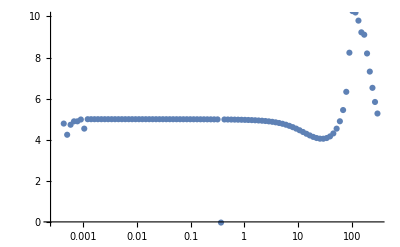

```mathematica
fitdeltampimub550=Transpose[{mpi[[3;;Length[h]-3]],Transpose[fitdeltamub550][[2]]}];
ListPlot[fitdeltampimub550,ScalingFunctions->{"Log"},PlotRange->{All,{0,10}}]
```

```mathematica
Export["NLOdeltamub550.dat",fitdeltampimub550]
```

NLOdeltamub550.dat